```mathematica
Pane[Grid[{
{Style["Simulation of HD2 IDA thermodynamics","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Simulation of HD2 IDA thermodynamics
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];
(*set values*)
h0fixed=1; d0fixed=1;kequhd2fixed=1;kequhgafixed=2;sighdfixed=1;sigdfixed=1;sig0fixed=1;
h0error=0; d0error=0;kequhd2error=0;kequhgaerror=0;sighderror=0;sigderror=0;sig0error=0;
(* Load Packges*)	
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoCacheHDD-Comp","thermoHD2-IDA1.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","styles.m"}]];
(* Paths*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHD2-IDA1.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHD2-IDA1.mx"}];

initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhd2in=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
	ga0in=initialparameters[[8]];
	kequhgain=initialparameters[[9]];

(*Buttons
*)

cachebutton=MouseAppearance[Button[stylesButtonGenericStyle["Cache Parameters","Caches the parameter's values for transfer"],{
cacheparameters={
h0in,
d0in,
kequhdin,
sig0in,
sigdin,
sighdin
},Export[cachePath,cacheparameters]},Appearance->None],"LinkHand"];

retrievebutton=MouseAppearance[Button[stylesButtonGenericStyle["Retrieve Cache","Retrieves the caches parameters from any notebook"],{
cacheparameters=Import[cachePath],
	h0in=cacheparameters[[1]],
	d0in=cacheparameters[[2]],
	kequhdin=cacheparameters[[3]],
	sig0in=cacheparameters[[4]],
	sigdin=cacheparameters[[5]],
	sighdin=cacheparameters[[6]]
	},Appearance->None],"LinkHand"];



simulationbutton=MouseAppearance[Button[stylesButtonGenericStyle["Simulate","Simulate a titration curve"],{ nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHD2IDA",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"];

variablessavebutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Parameters","Saves the set values of the parameters"],{
initialparameters={
h0in,
d0in,
step,
kequhd2in,
sig0in,
sigdin,
sighdin,
ga0in,
kequhgain
},Export[tempPath,initialparameters]},Appearance->None],"LinkHand"];
variablesloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Saved Parameters","Loads the previously saved values"],{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhd2in=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->None],"LinkHand"];

defaultloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Default Parameters","Loads the default values of the parameters"],{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhd2in=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->None],"LinkHand"];

inputline = {
   {
   Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 8],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 8],"M"},
 {"",Dynamic[h0in*1000000],"μM","c-step","","",""},
 
 {Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right], 
   InputField[Dynamic[d0in], FieldSize -> 8],"M",Style["K_equ(HD_2)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhd2in], FieldSize -> 8],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhd2in]],""},
 
 
 
   {Style["Guest:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[ga0in], FieldSize -> 8],"M",Style["K_equ(HG)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhgain], FieldSize -> 8],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[ga0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhgain]],""},
   
   
   {Style["Signal-HD_2", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 8],"",
   
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 8],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 8]},
      {"HD complex","","","dye alone","","","Startsignal"}  
    
};

Print[TableForm[{{simulationbutton,variablesloadbutton,variablessavebutton,defaultloadbutton,cachebutton,retrievebutton}}]];


Style[Grid[inputline,Alignment->Left],"Subsubsection",Black,FontSize->18]
```

Simulate | Load Saved Parameters | Save Parameters | Load Default Parameters | Cache Parameters | Retrieve Cache

species | concentration |  | binding |  |  |  | 
Host: |  | M | c-step  |  | M |  | 
 |  | μM | c-step |  |  |  | 
Dye: |  | M | K_equ(HD_2) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Guest: |  | M | K_equ(HG) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Signal-HD_2 |  |  | Signal-D |  |  | Signal-0 | 
HD complex |  |  | dye alone |  |  | Startsignal |

```mathematica
mode="Ga0 varied";
datasignal=sthd2IDAcacheSignalData[kequhd2in,kequhgain,h0in,d0in,ga0in,sig0in,sighdin,sigdin,step];
dataHD2=sthd2IDAcacheHD2Data[kequhd2in,kequhgain,h0in,d0in,ga0in,step];
dataD=sthd2IDAcacheDData[kequhd2in,kequhgain,h0in,d0in,ga0in,step];
dataHGa={{}};
dataGa={{}};

inputs={{"Quantity","Value"},
{"Mode",mode},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(HD2)",kequhd2in},
{"conc(G)",ga0in},
{"Kequ(HG)",kequhgain},
{"Signal-0",sig0in},
{"Signal-HD",sighdin},
{"Signal-Dye",sigdin},
{"c-step",step}
};
header={"conc","Signal"};
units={"M","INT"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];

(*signaloutput=Join[datasignal,List/@datathermohd[[All,2]],List/@datathermohdd[[All,2]],List/@datathermohga[[All,2]],List/@datathermod[[All,2]],List/@datathermoga[[All,2]],List/@datathermoh[[All,2]],2];*)

signaloutput=datasignal;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];


Quiet[exportbutton2=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];
simplot2=Manipulate[Show[ListLinePlot[{a1*datasignal,a2*dataHD2,a3*dataD,a4*dataHGa,a5*dataGa},
Epilog->{Text[Style["[H]_0",9],{h0in,h0in}],Text[Style["1/2[H]_0",9],{1/2*h0in,h0in}],Text[Style["3/2[H]_0",9],{3/2*h0in,h0in}],Text[Style["2[H]_0",9],{2*h0in,h0in}]},
PlotRange->All,PlotLegends->{"Signal","[HD_2]","[D]","[HG_A]","[G_A]","[H]"}],ImageSize-> Large,AxesOrigin->{0,0},GridLines->{{{h0in,Red},{2*h0in,Green},{1/2*h0in,Blue},{3/2*h0in,Black}},{}},PlotLabel-> "Simulated Data" ],{{a1,1,"Signal"},{1,0}},{{a2,0,"[HD_2]"},{1,0}},{{a3,0,"[D]"},{1,0}},{{a4,0,"[HG_A]"},{1,0}},{{a5,0,"[G_A]"},{1,0}},ControlPlacement->Right];

Print[simplot2,TableForm[{"You can save simulated data:",exportbutton2}]];

Off[Export::chtype];
```

You can save simulated data:
Save-Sim

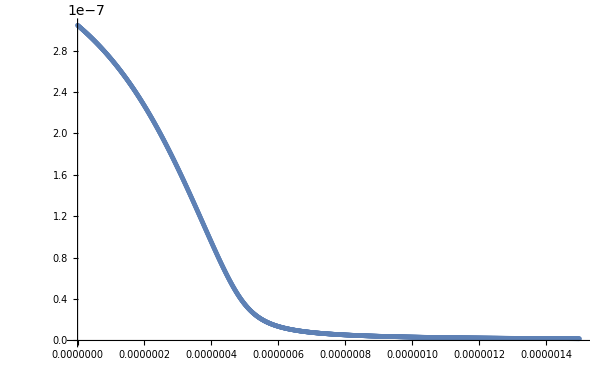

```mathematica
datasignal//ListPlot
```

```mathematica
stoich=0;

	ymax=Max[datasignal[[All,2]]];
	ymin=Min[datasignal[[All,2]]];

stoich1:=Module[{linpart1,linpart2,linfit1,linfit2,stoichdata1},
stoichdata1=datasignal/.{x_,y_}-> {x/h0in,normalize[y,ymax,ymin,2]};
	
linpart1 =Take[stoichdata1,IntegerPart[(Length[stoichdata1]*0.5)]];
linpart2 =Take[stoichdata1,-IntegerPart[(Length[stoichdata1]*0.3)]];
	linfit1=LinearModelFit[linpart1,x,x];
linfit2=LinearModelFit[linpart2,x,x];
Show[Plot[linfit1[x],{x,0,1.15},PlotStyle->{Gray,Thin}],Plot[linfit2[x],{x,0.5,3},PlotStyle->{Gray,Thin}],ListPlot[stoichdata1], GridLines->{{1},{1}},PlotRange-> All,PlotLabel-> Style["Molar Fraction","Subsection"]]

];
stoichiometrybutton=MouseAppearance[Button[stylesButtonGenericStyle["Stoichiometry","Display the Molar Fraction of the data"],Dynamic[If[stoich==1,stoich=0,stoich=1]],Appearance->None],"LinkHand"];
Print[stoichiometrybutton]
Dynamic[If[stoich==1,stoich1,""]]
```

Stoichiometry

```mathematica
stoichodata=datasignal/.{x_,y_}-> {x/h0in,normalize[y,ymax,ymin,2]};
linopart=IntegerPart[Dimensions[stoichodata][[1]]*1];
stoichodata[[Range[linopart]]];
a=stoichodata[[Range[linopart]]];
Take[a,-4]//TableForm
```

3.994 | 7.36299×10^-6
3.996 | 4.90542×10^-6
3.998 | 2.45109×10^-6
4. | -3.90313×10^-17

```mathematica
Position[a,0.04134958896306453]
```

{{600,2}}

```mathematica
IntegerPart[(Length[a]*0.3)]
```

600

```mathematica
LinearModelFit[a,x,x]
```

FittedModel[1.07323-0.923337 x]

```mathematica
a=Take[stoichodata,IntegerPart[(Length[stoichodata]*0.3)]];
```

```mathematica
stoichodata[[Range[a]]]
```

Part::pkspec1: The expression … cannot be used as a part specification.

{{0.,1.},{0.002,0.999095},{0.004,0.998187},{0.006,0.997276},{0.008,0.996362},{0.01,0.995446},{0.012,0.994526},{0.014,0.993603},{0.016,0.992677},{0.018,0.991748},{0.02,0.990815},1980,{3.982,0.000022177},{3.984,0.0000196998},{3.986,0.0000172259},{3.988,0.0000147553},{3.99,0.0000122879},{3.992,9.82383×10^-6},{3.994,7.36299×10^-6},{3.996,4.90542×10^-6},{3.998,2.45109×10^-6},{4.,-3.90313×10^-17}}⟦{1}⟧
 |  |  |  |

```mathematica
a//TableForm
```

0. | 1.
0.002 | 0.999095
0.004 | 0.998187
0.006 | 0.997276
0.008 | 0.996362
0.01 | 0.995446
0.012 | 0.994526
0.014 | 0.993603
0.016 | 0.992677
0.018 | 0.991748
0.02 | 0.990815
0.022 | 0.98988
0.024 | 0.988942
0.026 | 0.988
0.028 | 0.987056
0.03 | 0.986108
0.032 | 0.985157
0.034 | 0.984203
0.036 | 0.983246
0.038 | 0.982285
0.04 | 0.981322
0.042 | 0.980355
0.044 | 0.979385
0.046 | 0.978412
0.048 | 0.977435
0.05 | 0.976455
0.052 | 0.975472
0.054 | 0.974486
0.056 | 0.973496
0.058 | 0.972503
0.06 | 0.971507
0.062 | 0.970507
0.064 | 0.969504
0.066 | 0.968497
0.068 | 0.967488
0.07 | 0.966474
0.072 | 0.965458
0.074 | 0.964438
0.076 | 0.963414
0.078 | 0.962387
0.08 | 0.961357
0.082 | 0.960323
0.084 | 0.959286
0.086 | 0.958245
0.088 | 0.957201
0.09 | 0.956153
0.092 | 0.955102
0.094 | 0.954047
0.096 | 0.952988
0.098 | 0.951926
0.1 | 0.95086
0.102 | 0.949791
0.104 | 0.948718
0.106 | 0.947642
0.108 | 0.946562
0.11 | 0.945478
0.112 | 0.94439
0.114 | 0.943299
0.116 | 0.942204
0.118 | 0.941106
0.12 | 0.940003
0.122 | 0.938897
0.124 | 0.937787
0.126 | 0.936674
0.128 | 0.935557
0.13 | 0.934435
0.132 | 0.933311
0.134 | 0.932182
0.136 | 0.931049
0.138 | 0.929913
0.14 | 0.928772
0.142 | 0.927628
0.144 | 0.92648
0.146 | 0.925328
0.148 | 0.924173
0.15 | 0.923013
0.152 | 0.921849
0.154 | 0.920681
0.156 | 0.91951
0.158 | 0.918334
0.16 | 0.917155
0.162 | 0.915971
0.164 | 0.914783
0.166 | 0.913592
0.168 | 0.912396
0.17 | 0.911196
0.172 | 0.909992
0.174 | 0.908785
0.176 | 0.907573
0.178 | 0.906356
0.18 | 0.905136
0.182 | 0.903912
0.184 | 0.902683
0.186 | 0.901451
0.188 | 0.900214
0.19 | 0.898973
0.192 | 0.897727
0.194 | 0.896478
0.196 | 0.895224
0.198 | 0.893966
0.2 | 0.892704
0.202 | 0.891438
0.204 | 0.890167
0.206 | 0.888892
0.208 | 0.887612
0.21 | 0.886329
0.212 | 0.885041
0.214 | 0.883748
0.216 | 0.882452
0.218 | 0.881151
0.22 | 0.879845
0.222 | 0.878535
0.224 | 0.877221
0.226 | 0.875902
0.228 | 0.874579
0.23 | 0.873252
0.232 | 0.87192
0.234 | 0.870583
0.236 | 0.869242
0.238 | 0.867897
0.24 | 0.866547
0.242 | 0.865192
0.244 | 0.863833
0.246 | 0.86247
0.248 | 0.861102
0.25 | 0.859729
0.252 | 0.858352
0.254 | 0.85697
0.256 | 0.855583
0.258 | 0.854192
0.26 | 0.852797
0.262 | 0.851396
0.264 | 0.849991
0.266 | 0.848582
0.268 | 0.847168
0.27 | 0.845749
0.272 | 0.844325
0.274 | 0.842897
0.276 | 0.841464
0.278 | 0.840026
0.28 | 0.838583
0.282 | 0.837136
0.284 | 0.835684
0.286 | 0.834228
0.288 | 0.832766
0.29 | 0.8313
0.292 | 0.829829
0.294 | 0.828353
0.296 | 0.826872
0.298 | 0.825387
0.3 | 0.823896
0.302 | 0.822401
0.304 | 0.820901
0.306 | 0.819396
0.308 | 0.817886
0.31 | 0.816372
0.312 | 0.814852
0.314 | 0.813328
0.316 | 0.811799
0.318 | 0.810264
0.32 | 0.808725
0.322 | 0.807181
0.324 | 0.805632
0.326 | 0.804078
0.328 | 0.802519
0.33 | 0.800956
0.332 | 0.799387
0.334 | 0.797813
0.336 | 0.796234
0.338 | 0.794651
0.34 | 0.793062
0.342 | 0.791468
0.344 | 0.789869
0.346 | 0.788266
0.348 | 0.786657
0.35 | 0.785043
0.352 | 0.783424
0.354 | 0.7818
0.356 | 0.780172
0.358 | 0.778538
0.36 | 0.776899
0.362 | 0.775255
0.364 | 0.773605
0.366 | 0.771951
0.368 | 0.770292
0.37 | 0.768628
0.372 | 0.766958
0.374 | 0.765284
0.376 | 0.763604
0.378 | 0.761919
0.38 | 0.76023
0.382 | 0.758535
0.384 | 0.756835
0.386 | 0.75513
0.388 | 0.75342
0.39 | 0.751704
0.392 | 0.749984
0.394 | 0.748258
0.396 | 0.746528
0.398 | 0.744792
0.4 | 0.743051
0.402 | 0.741305
0.404 | 0.739554
0.406 | 0.737798
0.408 | 0.736036
0.41 | 0.73427
0.412 | 0.732498
0.414 | 0.730722
0.416 | 0.72894
0.418 | 0.727153
0.42 | 0.725361
0.422 | 0.723563
0.424 | 0.721761
0.426 | 0.719954
0.428 | 0.718141
0.43 | 0.716323
0.432 | 0.7145
0.434 | 0.712672
0.436 | 0.710839
0.438 | 0.709001
0.44 | 0.707158
0.442 | 0.70531
0.444 | 0.703456
0.446 | 0.701598
0.448 | 0.699734
0.45 | 0.697865
0.452 | 0.695991
0.454 | 0.694112
0.456 | 0.692228
0.458 | 0.690339
0.46 | 0.688445
0.462 | 0.686546
0.464 | 0.684642
0.466 | 0.682733
0.468 | 0.680818
0.47 | 0.678899
0.472 | 0.676975
0.474 | 0.675045
0.476 | 0.673111
0.478 | 0.671172
0.48 | 0.669227
0.482 | 0.667278
0.484 | 0.665324
0.486 | 0.663364
0.488 | 0.6614
0.49 | 0.659431
0.492 | 0.657457
0.494 | 0.655478
0.496 | 0.653494
0.498 | 0.651505
0.5 | 0.649511
0.502 | 0.647512
0.504 | 0.645509
0.506 | 0.6435
0.508 | 0.641487
0.51 | 0.639469
0.512 | 0.637446
0.514 | 0.635418
0.516 | 0.633386
0.518 | 0.631348
0.52 | 0.629306
0.522 | 0.627259
0.524 | 0.625208
0.526 | 0.623151
0.528 | 0.62109
0.53 | 0.619024
0.532 | 0.616954
0.534 | 0.614879
0.536 | 0.612799
0.538 | 0.610715
0.54 | 0.608626
0.542 | 0.606532
0.544 | 0.604434
0.546 | 0.602331
0.548 | 0.600224
0.55 | 0.598112
0.552 | 0.595996
0.554 | 0.593875
0.556 | 0.591749
0.558 | 0.58962
0.56 | 0.587485
0.562 | 0.585347
0.564 | 0.583204
0.566 | 0.581057
0.568 | 0.578905
0.57 | 0.576749
0.572 | 0.574589
0.574 | 0.572424
0.576 | 0.570255
0.578 | 0.568082
0.58 | 0.565905
0.582 | 0.563723
0.584 | 0.561538
0.586 | 0.559348
0.588 | 0.557154
0.59 | 0.554956
0.592 | 0.552754
0.594 | 0.550548
0.596 | 0.548338
0.598 | 0.546124
0.6 | 0.543906
0.602 | 0.541684
0.604 | 0.539459
0.606 | 0.537229
0.608 | 0.534996
0.61 | 0.532758
0.612 | 0.530518
0.614 | 0.528273
0.616 | 0.526024
0.618 | 0.523772
0.62 | 0.521516
0.622 | 0.519257
0.624 | 0.516994
0.626 | 0.514728
0.628 | 0.512458
0.63 | 0.510184
0.632 | 0.507907
0.634 | 0.505627
0.636 | 0.503343
0.638 | 0.501056
0.64 | 0.498766
0.642 | 0.496472
0.644 | 0.494175
0.646 | 0.491875
0.648 | 0.489572
0.65 | 0.487266
0.652 | 0.484957
0.654 | 0.482644
0.656 | 0.480329
0.658 | 0.478011
0.66 | 0.47569
0.662 | 0.473366
0.664 | 0.471039
0.666 | 0.468709
0.668 | 0.466377
0.67 | 0.464042
0.672 | 0.461704
0.674 | 0.459364
0.676 | 0.457021
0.678 | 0.454676
0.68 | 0.452328
0.682 | 0.449978
0.684 | 0.447626
0.686 | 0.445271
0.688 | 0.442914
0.69 | 0.440555
0.692 | 0.438193
0.694 | 0.43583
0.696 | 0.433465
0.698 | 0.431097
0.7 | 0.428728
0.702 | 0.426357
0.704 | 0.423984
0.706 | 0.421609
0.708 | 0.419232
0.71 | 0.416854
0.712 | 0.414475
0.714 | 0.412094
0.716 | 0.409711
0.718 | 0.407327
0.72 | 0.404942
0.722 | 0.402555
0.724 | 0.400167
0.726 | 0.397779
0.728 | 0.395389
0.73 | 0.392998
0.732 | 0.390606
0.734 | 0.388213
0.736 | 0.38582
0.738 | 0.383426
0.74 | 0.381031
0.742 | 0.378636
0.744 | 0.37624
0.746 | 0.373844
0.748 | 0.371448
0.75 | 0.369051
0.752 | 0.366655
0.754 | 0.364258
0.756 | 0.361861
0.758 | 0.359464
0.76 | 0.357068
0.762 | 0.354672
0.764 | 0.352276
0.766 | 0.34988
0.768 | 0.347486
0.77 | 0.345091
0.772 | 0.342698
0.774 | 0.340306
0.776 | 0.337914
0.778 | 0.335523
0.78 | 0.333134
0.782 | 0.330746
0.784 | 0.328359
0.786 | 0.325974
0.788 | 0.32359
0.79 | 0.321208
0.792 | 0.318828
0.794 | 0.316449
0.796 | 0.314073
0.798 | 0.311699
0.8 | 0.309327
0.802 | 0.306958
0.804 | 0.304591
0.806 | 0.302226
0.808 | 0.299865
0.81 | 0.297506
0.812 | 0.29515
0.814 | 0.292798
0.816 | 0.290448
0.818 | 0.288103
0.82 | 0.28576
0.822 | 0.283422
0.824 | 0.281087
0.826 | 0.278756
0.828 | 0.27643
0.83 | 0.274108
0.832 | 0.27179
0.834 | 0.269477
0.836 | 0.267168
0.838 | 0.264865
0.84 | 0.262566
0.842 | 0.260273
0.844 | 0.257985
0.846 | 0.255703
0.848 | 0.253427
0.85 | 0.251156
0.852 | 0.248892
0.854 | 0.246633
0.856 | 0.244382
0.858 | 0.242136
0.86 | 0.239898
0.862 | 0.237667
0.864 | 0.235442
0.866 | 0.233226
0.868 | 0.231016
0.87 | 0.228815
0.872 | 0.226621
0.874 | 0.224436
0.876 | 0.222258
0.878 | 0.22009
0.88 | 0.21793
0.882 | 0.215779
0.884 | 0.213637
0.886 | 0.211504
0.888 | 0.209381
0.89 | 0.207267
0.892 | 0.205164
0.894 | 0.20307
0.896 | 0.200987
0.898 | 0.198915
0.9 | 0.196853
0.902 | 0.194802
0.904 | 0.192762
0.906 | 0.190734
0.908 | 0.188717
0.91 | 0.186712
0.912 | 0.184719
0.914 | 0.182738
0.916 | 0.180769
0.918 | 0.178813
0.92 | 0.176869
0.922 | 0.174939
0.924 | 0.173022
0.926 | 0.171118
0.928 | 0.169227
0.93 | 0.16735
0.932 | 0.165487
0.934 | 0.163638
0.936 | 0.161803
0.938 | 0.159983
0.94 | 0.158177
0.942 | 0.156386
0.944 | 0.154609
0.946 | 0.152848
0.948 | 0.151102
0.95 | 0.149371
0.952 | 0.147655
0.954 | 0.145955
0.956 | 0.144271
0.958 | 0.142602
0.96 | 0.140949
0.962 | 0.139313
0.964 | 0.137692
0.966 | 0.136087
0.968 | 0.134499
0.97 | 0.132927
0.972 | 0.131371
0.974 | 0.129832
0.976 | 0.12831
0.978 | 0.126803
0.98 | 0.125314
0.982 | 0.123841
0.984 | 0.122385
0.986 | 0.120945
0.988 | 0.119522
0.99 | 0.118116
0.992 | 0.116726
0.994 | 0.115353
0.996 | 0.113996
0.998 | 0.112656
1. | 0.111333
1.002 | 0.110026
1.004 | 0.108736
1.006 | 0.107462
1.008 | 0.106204
1.01 | 0.104963
1.012 | 0.103738
1.014 | 0.102529
1.016 | 0.101336
1.018 | 0.100158
1.02 | 0.0989972
1.022 | 0.0978516
1.024 | 0.0967216
1.026 | 0.0956071
1.028 | 0.094508
1.03 | 0.0934242
1.032 | 0.0923555
1.034 | 0.0913017
1.036 | 0.0902628
1.038 | 0.0892386
1.04 | 0.088229
1.042 | 0.0872339
1.044 | 0.086253
1.046 | 0.0852862
1.048 | 0.0843334
1.05 | 0.0833944
1.052 | 0.0824691
1.054 | 0.0815572
1.056 | 0.0806587
1.058 | 0.0797734
1.06 | 0.0789011
1.062 | 0.0780416
1.064 | 0.0771948
1.066 | 0.0763605
1.068 | 0.0755386
1.07 | 0.0747288
1.072 | 0.0739311
1.074 | 0.0731451
1.076 | 0.0723709
1.078 | 0.0716082
1.08 | 0.0708568
1.082 | 0.0701165
1.084 | 0.0693873
1.086 | 0.068669
1.088 | 0.0679613
1.09 | 0.0672641
1.092 | 0.0665773
1.094 | 0.0659007
1.096 | 0.0652341
1.098 | 0.0645774
1.1 | 0.0639304
1.102 | 0.063293
1.104 | 0.0626649
1.106 | 0.0620462
1.108 | 0.0614366
1.11 | 0.0608359
1.112 | 0.060244
1.114 | 0.0596609
1.116 | 0.0590862
1.118 | 0.0585199
1.12 | 0.0579619
1.122 | 0.057412
1.124 | 0.05687
1.126 | 0.0563359
1.128 | 0.0558095
1.13 | 0.0552906
1.132 | 0.0547793
1.134 | 0.0542752
1.136 | 0.0537783
1.138 | 0.0532885
1.14 | 0.0528056
1.142 | 0.0523296
1.144 | 0.0518603
1.146 | 0.0513976
1.148 | 0.0509414
1.15 | 0.0504915
1.152 | 0.0500479
1.154 | 0.0496105
1.156 | 0.0491791
1.158 | 0.0487537
1.16 | 0.0483342
1.162 | 0.0479203
1.164 | 0.0475121
1.166 | 0.0471095
1.168 | 0.0467123
1.17 | 0.0463205
1.172 | 0.045934
1.174 | 0.0455526
1.176 | 0.0451763
1.178 | 0.0448051
1.18 | 0.0444387
1.182 | 0.0440772
1.184 | 0.0437204
1.186 | 0.0433683
1.188 | 0.0430208
1.19 | 0.0426779
1.192 | 0.0423393
1.194 | 0.0420051
1.196 | 0.0416753
1.198 | 0.0413496
1.2 | 0.0410281
1.202 | 0.0407106
1.204 | 0.0403972
1.206 | 0.0400877
1.208 | 0.0397821
1.21 | 0.0394803
1.212 | 0.0391823
1.214 | 0.0388879
1.216 | 0.0385972
1.218 | 0.03831
1.22 | 0.0380264
1.222 | 0.0377462
1.224 | 0.0374694
1.226 | 0.0371959
1.228 | 0.0369257
1.23 | 0.0366588
1.232 | 0.036395
1.234 | 0.0361344
1.236 | 0.0358768
1.238 | 0.0356223
1.24 | 0.0353708
1.242 | 0.0351222
1.244 | 0.0348765
1.246 | 0.0346336
1.248 | 0.0343935
1.25 | 0.0341562
1.252 | 0.0339216
1.254 | 0.0336897
1.256 | 0.0334603
1.258 | 0.0332336
1.26 | 0.0330094
1.262 | 0.0327878
1.264 | 0.0325686
1.266 | 0.0323518
1.268 | 0.0321374
1.27 | 0.0319254
1.272 | 0.0317157
1.274 | 0.0315083
1.276 | 0.0313031
1.278 | 0.0311002
1.28 | 0.0308994
1.282 | 0.0307008
1.284 | 0.0305043
1.286 | 0.0303099
1.288 | 0.0301176
1.29 | 0.0299273
1.292 | 0.0297389
1.294 | 0.0295526
1.296 | 0.0293682
1.298 | 0.0291857
1.3 | 0.0290051
1.302 | 0.0288263
1.304 | 0.0286494
1.306 | 0.0284743
1.308 | 0.0283009
1.31 | 0.0281293
1.312 | 0.0279595
1.314 | 0.0277913
1.316 | 0.0276248
1.318 | 0.02746
1.32 | 0.0272968
1.322 | 0.0271352
1.324 | 0.0269752
1.326 | 0.0268168
1.328 | 0.0266599
1.33 | 0.0265045
1.332 | 0.0263507
1.334 | 0.0261983
1.336 | 0.0260474
1.338 | 0.0258979
1.34 | 0.0257498
1.342 | 0.0256032
1.344 | 0.0254579
1.346 | 0.025314
1.348 | 0.0251714
1.35 | 0.0250302
1.352 | 0.0248903
1.354 | 0.0247517
1.356 | 0.0246143
1.358 | 0.0244782
1.36 | 0.0243434
1.362 | 0.0242098
1.364 | 0.0240774
1.366 | 0.0239461
1.368 | 0.0238161
1.37 | 0.0236873
1.372 | 0.0235595
1.374 | 0.023433
1.376 | 0.0233075
1.378 | 0.0231832
1.38 | 0.0230599
1.382 | 0.0229377
1.384 | 0.0228166
1.386 | 0.0226966
1.388 | 0.0225776
1.39 | 0.0224596
1.392 | 0.0223426
1.394 | 0.0222266
1.396 | 0.0221116
1.398 | 0.0219976
1.4 | 0.0218846
1.402 | 0.0217725
1.404 | 0.0216614
1.406 | 0.0215512
1.408 | 0.0214419
1.41 | 0.0213335
1.412 | 0.021226
1.414 | 0.0211194
1.416 | 0.0210136
1.418 | 0.0209088
1.42 | 0.0208048
1.422 | 0.0207016
1.424 | 0.0205993
1.426 | 0.0204978
1.428 | 0.0203971
1.43 | 0.0202972
1.432 | 0.0201982
1.434 | 0.0200999
1.436 | 0.0200024
1.438 | 0.0199056
1.44 | 0.0198096
1.442 | 0.0197144
1.444 | 0.0196199
1.446 | 0.0195262
1.448 | 0.0194332
1.45 | 0.0193409
1.452 | 0.0192493
1.454 | 0.0191584
1.456 | 0.0190682
1.458 | 0.0189787
1.46 | 0.0188899
1.462 | 0.0188017
1.464 | 0.0187143
1.466 | 0.0186274
1.468 | 0.0185413
1.47 | 0.0184557
1.472 | 0.0183708
1.474 | 0.0182866
1.476 | 0.0182029
1.478 | 0.0181199
1.48 | 0.0180375
1.482 | 0.0179557
1.484 | 0.0178745
1.486 | 0.0177939
1.488 | 0.0177138
1.49 | 0.0176344
1.492 | 0.0175555
1.494 | 0.0174771
1.496 | 0.0173994
1.498 | 0.0173222
1.5 | 0.0172455
1.502 | 0.0171694
1.504 | 0.0170938
1.506 | 0.0170188
1.508 | 0.0169443
1.51 | 0.0168703
1.512 | 0.0167968
1.514 | 0.0167238
1.516 | 0.0166513
1.518 | 0.0165794
1.52 | 0.0165079
1.522 | 0.0164369
1.524 | 0.0163664
1.526 | 0.0162964
1.528 | 0.0162269
1.53 | 0.0161578
1.532 | 0.0160892
1.534 | 0.0160211
1.536 | 0.0159534
1.538 | 0.0158861
1.54 | 0.0158194
1.542 | 0.015753
1.544 | 0.0156871
1.546 | 0.0156217
1.548 | 0.0155566
1.55 | 0.015492
1.552 | 0.0154278
1.554 | 0.0153641
1.556 | 0.0153007
1.558 | 0.0152378
1.56 | 0.0151752
1.562 | 0.0151131
1.564 | 0.0150514
1.566 | 0.0149901
1.568 | 0.0149291
1.57 | 0.0148686
1.572 | 0.0148084
1.574 | 0.0147486
1.576 | 0.0146892
1.578 | 0.0146301
1.58 | 0.0145715
1.582 | 0.0145132
1.584 | 0.0144552
1.586 | 0.0143977
1.588 | 0.0143405
1.59 | 0.0142836
1.592 | 0.0142271
1.594 | 0.0141709
1.596 | 0.0141151
1.598 | 0.0140596
1.6 | 0.0140045
1.602 | 0.0139496
1.604 | 0.0138952
1.606 | 0.013841
1.608 | 0.0137872
1.61 | 0.0137337
1.612 | 0.0136805
1.614 | 0.0136277
1.616 | 0.0135751
1.618 | 0.0135229
1.62 | 0.013471
1.622 | 0.0134194
1.624 | 0.013368
1.626 | 0.013317
1.628 | 0.0132663
1.63 | 0.0132159
1.632 | 0.0131658
1.634 | 0.013116
1.636 | 0.0130664
1.638 | 0.0130172
1.64 | 0.0129682
1.642 | 0.0129195
1.644 | 0.0128711
1.646 | 0.012823
1.648 | 0.0127751
1.65 | 0.0127275
1.652 | 0.0126802
1.654 | 0.0126331
1.656 | 0.0125863
1.658 | 0.0125398
1.66 | 0.0124936
1.662 | 0.0124476
1.664 | 0.0124018
1.666 | 0.0123563
1.668 | 0.0123111
1.67 | 0.0122661
1.672 | 0.0122214
1.674 | 0.0121769
1.676 | 0.0121326
1.678 | 0.0120886
1.68 | 0.0120448
1.682 | 0.0120013
1.684 | 0.011958
1.686 | 0.011915
1.688 | 0.0118721
1.69 | 0.0118295
1.692 | 0.0117872
1.694 | 0.011745
1.696 | 0.0117031
1.698 | 0.0116614
1.7 | 0.01162
1.702 | 0.0115787
1.704 | 0.0115377
1.706 | 0.0114969
1.708 | 0.0114563
1.71 | 0.0114159
1.712 | 0.0113757
1.714 | 0.0113358
1.716 | 0.011296
1.718 | 0.0112565
1.72 | 0.0112171
1.722 | 0.011178
1.724 | 0.0111391
1.726 | 0.0111003
1.728 | 0.0110618
1.73 | 0.0110235
1.732 | 0.0109853
1.734 | 0.0109474
1.736 | 0.0109096
1.738 | 0.0108721
1.74 | 0.0108347
1.742 | 0.0107975
1.744 | 0.0107605
1.746 | 0.0107237
1.748 | 0.0106871
1.75 | 0.0106506
1.752 | 0.0106144
1.754 | 0.0105783
1.756 | 0.0105424
1.758 | 0.0105067
1.76 | 0.0104711
1.762 | 0.0104357
1.764 | 0.0104006
1.766 | 0.0103655
1.768 | 0.0103307
1.77 | 0.010296
1.772 | 0.0102615
1.774 | 0.0102271
1.776 | 0.010193
1.778 | 0.0101589
1.78 | 0.0101251
1.782 | 0.0100914
1.784 | 0.0100579
1.786 | 0.0100245
1.788 | 0.00999132
1.79 | 0.00995827
1.792 | 0.00992538
1.794 | 0.00989265
1.796 | 0.00986008
1.798 | 0.00982765
1.8 | 0.00979538
1.802 | 0.00976327
1.804 | 0.0097313
1.806 | 0.00969948
1.808 | 0.00966782
1.81 | 0.0096363
1.812 | 0.00960492
1.814 | 0.00957369
1.816 | 0.00954261
1.818 | 0.00951167
1.82 | 0.00948087
1.822 | 0.00945022
1.824 | 0.0094197
1.826 | 0.00938933
1.828 | 0.00935909
1.83 | 0.009329
1.832 | 0.00929904
1.834 | 0.00926921
1.836 | 0.00923952
1.838 | 0.00920997
1.84 | 0.00918054
1.842 | 0.00915126
1.844 | 0.0091221
1.846 | 0.00909307
1.848 | 0.00906417
1.85 | 0.0090354
1.852 | 0.00900676
1.854 | 0.00897825
1.856 | 0.00894986
1.858 | 0.0089216
1.86 | 0.00889347
1.862 | 0.00886546
1.864 | 0.00883757
1.866 | 0.0088098
1.868 | 0.00878215
1.87 | 0.00875463
1.872 | 0.00872723
1.874 | 0.00869994
1.876 | 0.00867277
1.878 | 0.00864572
1.88 | 0.00861879
1.882 | 0.00859198
1.884 | 0.00856528
1.886 | 0.00853869
1.888 | 0.00851222
1.89 | 0.00848586
1.892 | 0.00845961
1.894 | 0.00843348
1.896 | 0.00840745
1.898 | 0.00838154
1.9 | 0.00835574
1.902 | 0.00833004
1.904 | 0.00830446
1.906 | 0.00827898
1.908 | 0.00825361
1.91 | 0.00822834
1.912 | 0.00820318
1.914 | 0.00817813
1.916 | 0.00815318
1.918 | 0.00812833
1.92 | 0.00810359
1.922 | 0.00807895
1.924 | 0.00805441
1.926 | 0.00802997
1.928 | 0.00800563
1.93 | 0.0079814
1.932 | 0.00795726
1.934 | 0.00793322
1.936 | 0.00790928
1.938 | 0.00788543
1.94 | 0.00786169
1.942 | 0.00783804
1.944 | 0.00781448
1.946 | 0.00779102
1.948 | 0.00776766
1.95 | 0.00774438
1.952 | 0.00772121
1.954 | 0.00769812
1.956 | 0.00767513
1.958 | 0.00765223
1.96 | 0.00762942
1.962 | 0.0076067
1.964 | 0.00758408
1.966 | 0.00756154
1.968 | 0.00753909
1.97 | 0.00751673
1.972 | 0.00749445
1.974 | 0.00747227
1.976 | 0.00745017
1.978 | 0.00742816
1.98 | 0.00740624
1.982 | 0.0073844
1.984 | 0.00736264
1.986 | 0.00734097
1.988 | 0.00731938
1.99 | 0.00729788
1.992 | 0.00727646
1.994 | 0.00725513
1.996 | 0.00723387
1.998 | 0.0072127
2. | 0.00719161
2.002 | 0.0071706
2.004 | 0.00714967
2.006 | 0.00712882
2.008 | 0.00710805
2.01 | 0.00708735
2.012 | 0.00706674
2.014 | 0.0070462
2.016 | 0.00702575
2.018 | 0.00700537
2.02 | 0.00698506
2.022 | 0.00696483
2.024 | 0.00694468
2.026 | 0.00692461
2.028 | 0.0069046
2.03 | 0.00688468
2.032 | 0.00686482
2.034 | 0.00684505
2.036 | 0.00682534
2.038 | 0.00680571
2.04 | 0.00678615
2.042 | 0.00676666
2.044 | 0.00674725
2.046 | 0.0067279
2.048 | 0.00670863
2.05 | 0.00668943
2.052 | 0.00667029
2.054 | 0.00665123
2.056 | 0.00663224
2.058 | 0.00661331
2.06 | 0.00659446
2.062 | 0.00657567
2.064 | 0.00655695
2.066 | 0.0065383
2.068 | 0.00651972
2.07 | 0.0065012
2.072 | 0.00648275
2.074 | 0.00646436
2.076 | 0.00644605
2.078 | 0.00642779
2.08 | 0.0064096
2.082 | 0.00639148
2.084 | 0.00637342
2.086 | 0.00635543
2.088 | 0.0063375
2.09 | 0.00631963
2.092 | 0.00630183
2.094 | 0.00628408
2.096 | 0.0062664
2.098 | 0.00624879
2.1 | 0.00623123
2.102 | 0.00621374
2.104 | 0.00619631
2.106 | 0.00617893
2.108 | 0.00616162
2.11 | 0.00614437
2.112 | 0.00612718
2.114 | 0.00611005
2.116 | 0.00609298
2.118 | 0.00607596
2.12 | 0.00605901
2.122 | 0.00604211
2.124 | 0.00602527
2.126 | 0.00600849
2.128 | 0.00599177
2.13 | 0.0059751
2.132 | 0.00595849
2.134 | 0.00594194
2.136 | 0.00592544
2.138 | 0.005909
2.14 | 0.00589262
2.142 | 0.00587629
2.144 | 0.00586001
2.146 | 0.0058438
2.148 | 0.00582763
2.15 | 0.00581152
2.152 | 0.00579546
2.154 | 0.00577946
2.156 | 0.00576351
2.158 | 0.00574762
2.16 | 0.00573178
2.162 | 0.00571599
2.164 | 0.00570025
2.166 | 0.00568456
2.168 | 0.00566893
2.17 | 0.00565335
2.172 | 0.00563782
2.174 | 0.00562234
2.176 | 0.00560691
2.178 | 0.00559153
2.18 | 0.00557621
2.182 | 0.00556093
2.184 | 0.00554571
2.186 | 0.00553053
2.188 | 0.0055154
2.19 | 0.00550032
2.192 | 0.00548529
2.194 | 0.00547031
2.196 | 0.00545538
2.198 | 0.0054405
2.2 | 0.00542566
2.202 | 0.00541087
2.204 | 0.00539613
2.206 | 0.00538144
2.208 | 0.0053668
2.21 | 0.0053522
2.212 | 0.00533764
2.214 | 0.00532314
2.216 | 0.00530868
2.218 | 0.00529427
2.22 | 0.0052799
2.222 | 0.00526558
2.224 | 0.0052513
2.226 | 0.00523707
2.228 | 0.00522288
2.23 | 0.00520874
2.232 | 0.00519464
2.234 | 0.00518059
2.236 | 0.00516658
2.238 | 0.00515262
2.24 | 0.00513869
2.242 | 0.00512482
2.244 | 0.00511098
2.246 | 0.00509719
2.248 | 0.00508344
2.25 | 0.00506974
2.252 | 0.00505607
2.254 | 0.00504245
2.256 | 0.00502887
2.258 | 0.00501534
2.26 | 0.00500184
2.262 | 0.00498839
2.264 | 0.00497497
2.266 | 0.0049616
2.268 | 0.00494827
2.27 | 0.00493498
2.272 | 0.00492173
2.274 | 0.00490852
2.276 | 0.00489536
2.278 | 0.00488223
2.28 | 0.00486914
2.282 | 0.00485609
2.284 | 0.00484308
2.286 | 0.00483011
2.288 | 0.00481718
2.29 | 0.00480429
2.292 | 0.00479143
2.294 | 0.00477862
2.296 | 0.00476584
2.298 | 0.0047531
2.3 | 0.0047404
2.302 | 0.00472774
2.304 | 0.00471512
2.306 | 0.00470253
2.308 | 0.00468998
2.31 | 0.00467747
2.312 | 0.00466499
2.314 | 0.00465256
2.316 | 0.00464016
2.318 | 0.00462779
2.32 | 0.00461546
2.322 | 0.00460317
2.324 | 0.00459091
2.326 | 0.0045787
2.328 | 0.00456651
2.33 | 0.00455436
2.332 | 0.00454225
2.334 | 0.00453017
2.336 | 0.00451813
2.338 | 0.00450612
2.34 | 0.00449415
2.342 | 0.00448221
2.344 | 0.00447031
2.346 | 0.00445844
2.348 | 0.0044466
2.35 | 0.0044348
2.352 | 0.00442304
2.354 | 0.00441131
2.356 | 0.00439961
2.358 | 0.00438794
2.36 | 0.00437631
2.362 | 0.00436471
2.364 | 0.00435314
2.366 | 0.00434161
2.368 | 0.00433011
2.37 | 0.00431865
2.372 | 0.00430721
2.374 | 0.00429581
2.376 | 0.00428444
2.378 | 0.0042731
2.38 | 0.0042618
2.382 | 0.00425052
2.384 | 0.00423928
2.386 | 0.00422807
2.388 | 0.00421689
2.39 | 0.00420574
2.392 | 0.00419463
2.394 | 0.00418354
2.396 | 0.00417249
2.398 | 0.00416146
2.4 | 0.00415047
2.402 | 0.00413951
2.404 | 0.00412858
2.406 | 0.00411767
2.408 | 0.0041068
2.41 | 0.00409596
2.412 | 0.00408515
2.414 | 0.00407437
2.416 | 0.00406362
2.418 | 0.00405289
2.42 | 0.0040422
2.422 | 0.00403154
2.424 | 0.0040209
2.426 | 0.0040103
2.428 | 0.00399972
2.43 | 0.00398917
2.432 | 0.00397866
2.434 | 0.00396817
2.436 | 0.0039577
2.438 | 0.00394727
2.44 | 0.00393687
2.442 | 0.00392649
2.444 | 0.00391614
2.446 | 0.00390582
2.448 | 0.00389553
2.45 | 0.00388526
2.452 | 0.00387502
2.454 | 0.00386481
2.456 | 0.00385463
2.458 | 0.00384448
2.46 | 0.00383435
2.462 | 0.00382425
2.464 | 0.00381417
2.466 | 0.00380412
2.468 | 0.0037941
2.47 | 0.00378411
2.472 | 0.00377414
2.474 | 0.0037642
2.476 | 0.00375429
2.478 | 0.0037444
2.48 | 0.00373453
2.482 | 0.0037247
2.484 | 0.00371489
2.486 | 0.0037051
2.488 | 0.00369534
2.49 | 0.00368561
2.492 | 0.0036759
2.494 | 0.00366622
2.496 | 0.00365656
2.498 | 0.00364693
2.5 | 0.00363732
2.502 | 0.00362774
2.504 | 0.00361818
2.506 | 0.00360865
2.508 | 0.00359914
2.51 | 0.00358966
2.512 | 0.0035802
2.514 | 0.00357076
2.516 | 0.00356135
2.518 | 0.00355197
2.52 | 0.00354261
2.522 | 0.00353327
2.524 | 0.00352396
2.526 | 0.00351467
2.528 | 0.0035054
2.53 | 0.00349616
2.532 | 0.00348694
2.534 | 0.00347774
2.536 | 0.00346857
2.538 | 0.00345942
2.54 | 0.0034503
2.542 | 0.0034412
2.544 | 0.00343212
2.546 | 0.00342306
2.548 | 0.00341403
2.55 | 0.00340502
2.552 | 0.00339603
2.554 | 0.00338706
2.556 | 0.00337812
2.558 | 0.0033692
2.56 | 0.0033603
2.562 | 0.00335143
2.564 | 0.00334258
2.566 | 0.00333374
2.568 | 0.00332494
2.57 | 0.00331615
2.572 | 0.00330738
2.574 | 0.00329864
2.576 | 0.00328992
2.578 | 0.00328122
2.58 | 0.00327254
2.582 | 0.00326388
2.584 | 0.00325525
2.586 | 0.00324663
2.588 | 0.00323804
2.59 | 0.00322947
2.592 | 0.00322092
2.594 | 0.00321239
2.596 | 0.00320388
2.598 | 0.00319539
2.6 | 0.00318692
2.602 | 0.00317847
2.604 | 0.00317005
2.606 | 0.00316164
2.608 | 0.00315326
2.61 | 0.00314489
2.612 | 0.00313655
2.614 | 0.00312822
2.616 | 0.00311992
2.618 | 0.00311164
2.62 | 0.00310337
2.622 | 0.00309513
2.624 | 0.00308691
2.626 | 0.0030787
2.628 | 0.00307052
2.63 | 0.00306235
2.632 | 0.00305421
2.634 | 0.00304608
2.636 | 0.00303798
2.638 | 0.00302989
2.64 | 0.00302182
2.642 | 0.00301377
2.644 | 0.00300574
2.646 | 0.00299773
2.648 | 0.00298974
2.65 | 0.00298177
2.652 | 0.00297382
2.654 | 0.00296588
2.656 | 0.00295797
2.658 | 0.00295007
2.66 | 0.00294219
2.662 | 0.00293433
2.664 | 0.00292649
2.666 | 0.00291867
2.668 | 0.00291087
2.67 | 0.00290308
2.672 | 0.00289531
2.674 | 0.00288756
2.676 | 0.00287983
2.678 | 0.00287212
2.68 | 0.00286443
2.682 | 0.00285675
2.684 | 0.00284909
2.686 | 0.00284145
2.688 | 0.00283382
2.69 | 0.00282622
2.692 | 0.00281863
2.694 | 0.00281106
2.696 | 0.00280351
2.698 | 0.00279597
2.7 | 0.00278845
2.702 | 0.00278095
2.704 | 0.00277347
2.706 | 0.002766
2.708 | 0.00275855
2.71 | 0.00275112
2.712 | 0.0027437
2.714 | 0.0027363
2.716 | 0.00272892
2.718 | 0.00272156
2.72 | 0.00271421
2.722 | 0.00270688
2.724 | 0.00269956
2.726 | 0.00269227
2.728 | 0.00268498
2.73 | 0.00267772
2.732 | 0.00267047
2.734 | 0.00266324
2.736 | 0.00265602
2.738 | 0.00264882
2.74 | 0.00264164
2.742 | 0.00263447
2.744 | 0.00262732
2.746 | 0.00262019
2.748 | 0.00261307
2.75 | 0.00260597
2.752 | 0.00259888
2.754 | 0.00259181
2.756 | 0.00258475
2.758 | 0.00257772
2.76 | 0.00257069
2.762 | 0.00256368
2.764 | 0.00255669
2.766 | 0.00254971
2.768 | 0.00254275
2.77 | 0.00253581
2.772 | 0.00252888
2.774 | 0.00252196
2.776 | 0.00251506
2.778 | 0.00250818
2.78 | 0.00250131
2.782 | 0.00249445
2.784 | 0.00248761
2.786 | 0.00248079
2.788 | 0.00247398
2.79 | 0.00246719
2.792 | 0.00246041
2.794 | 0.00245364
2.796 | 0.00244689
2.798 | 0.00244016
2.8 | 0.00243344
2.802 | 0.00242673
2.804 | 0.00242004
2.806 | 0.00241336
2.808 | 0.0024067
2.81 | 0.00240005
2.812 | 0.00239342
2.814 | 0.0023868
2.816 | 0.0023802
2.818 | 0.00237361
2.82 | 0.00236703
2.822 | 0.00236047
2.824 | 0.00235392
2.826 | 0.00234739
2.828 | 0.00234087
2.83 | 0.00233436
2.832 | 0.00232787
2.834 | 0.00232139
2.836 | 0.00231493
2.838 | 0.00230848
2.84 | 0.00230204
2.842 | 0.00229562
2.844 | 0.00228921
2.846 | 0.00228282
2.848 | 0.00227644
2.85 | 0.00227007
2.852 | 0.00226371
2.854 | 0.00225737
2.856 | 0.00225105
2.858 | 0.00224473
2.86 | 0.00223843
2.862 | 0.00223214
2.864 | 0.00222587
2.866 | 0.00221961
2.868 | 0.00221336
2.87 | 0.00220713
2.872 | 0.0022009
2.874 | 0.0021947
2.876 | 0.0021885
2.878 | 0.00218232
2.88 | 0.00217615
2.882 | 0.00216999
2.884 | 0.00216385
2.886 | 0.00215772
2.888 | 0.0021516
2.89 | 0.00214549
2.892 | 0.0021394
2.894 | 0.00213332
2.896 | 0.00212725
2.898 | 0.0021212
2.9 | 0.00211515
2.902 | 0.00210912
2.904 | 0.00210311
2.906 | 0.0020971
2.908 | 0.00209111
2.91 | 0.00208513
2.912 | 0.00207916
2.914 | 0.0020732
2.916 | 0.00206726
2.918 | 0.00206133
2.92 | 0.00205541
2.922 | 0.0020495
2.924 | 0.00204361
2.926 | 0.00203772
2.928 | 0.00203185
2.93 | 0.00202599
2.932 | 0.00202014
2.934 | 0.00201431
2.936 | 0.00200849
2.938 | 0.00200267
2.94 | 0.00199687
2.942 | 0.00199109
2.944 | 0.00198531
2.946 | 0.00197955
2.948 | 0.00197379
2.95 | 0.00196805
2.952 | 0.00196232
2.954 | 0.0019566
2.956 | 0.0019509
2.958 | 0.0019452
2.96 | 0.00193952
2.962 | 0.00193384
2.964 | 0.00192818
2.966 | 0.00192253
2.968 | 0.00191689
2.97 | 0.00191127
2.972 | 0.00190565
2.974 | 0.00190005
2.976 | 0.00189445
2.978 | 0.00188887
2.98 | 0.0018833
2.982 | 0.00187774
2.984 | 0.00187219
2.986 | 0.00186665
2.988 | 0.00186112
2.99 | 0.00185561
2.992 | 0.0018501
2.994 | 0.00184461
2.996 | 0.00183912
2.998 | 0.00183365
3. | 0.00182819
3.002 | 0.00182274
3.004 | 0.00181729
3.006 | 0.00181186
3.008 | 0.00180645
3.01 | 0.00180104
3.012 | 0.00179564
3.014 | 0.00179025
3.016 | 0.00178487
3.018 | 0.00177951
3.02 | 0.00177415
3.022 | 0.0017688
3.024 | 0.00176347
3.026 | 0.00175814
3.028 | 0.00175283
3.03 | 0.00174752
3.032 | 0.00174223
3.034 | 0.00173695
3.036 | 0.00173167
3.038 | 0.00172641
3.04 | 0.00172116
3.042 | 0.00171591
3.044 | 0.00171068
3.046 | 0.00170546
3.048 | 0.00170024
3.05 | 0.00169504
3.052 | 0.00168985
3.054 | 0.00168467
3.056 | 0.00167949
3.058 | 0.00167433
3.06 | 0.00166918
3.062 | 0.00166403
3.064 | 0.0016589
3.066 | 0.00165378
3.068 | 0.00164866
3.07 | 0.00164356
3.072 | 0.00163846
3.074 | 0.00163338
3.076 | 0.0016283
3.078 | 0.00162324
3.08 | 0.00161818
3.082 | 0.00161313
3.084 | 0.0016081
3.086 | 0.00160307
3.088 | 0.00159805
3.09 | 0.00159304
3.092 | 0.00158804
3.094 | 0.00158305
3.096 | 0.00157807
3.098 | 0.0015731
3.1 | 0.00156814
3.102 | 0.00156319
3.104 | 0.00155825
3.106 | 0.00155331
3.108 | 0.00154839
3.11 | 0.00154347
3.112 | 0.00153857
3.114 | 0.00153367
3.116 | 0.00152878
3.118 | 0.0015239
3.12 | 0.00151903
3.122 | 0.00151417
3.124 | 0.00150932
3.126 | 0.00150448
3.128 | 0.00149964
3.13 | 0.00149482
3.132 | 0.00149
3.134 | 0.0014852
3.136 | 0.0014804
3.138 | 0.00147561
3.14 | 0.00147083
3.142 | 0.00146606
3.144 | 0.0014613
3.146 | 0.00145654
3.148 | 0.0014518
3.15 | 0.00144706
3.152 | 0.00144233
3.154 | 0.00143761
3.156 | 0.0014329
3.158 | 0.0014282
3.16 | 0.00142351
3.162 | 0.00141882
3.164 | 0.00141414
3.166 | 0.00140948
3.168 | 0.00140482
3.17 | 0.00140017
3.172 | 0.00139552
3.174 | 0.00139089
3.176 | 0.00138626
3.178 | 0.00138165
3.18 | 0.00137704
3.182 | 0.00137244
3.184 | 0.00136785
3.186 | 0.00136326
3.188 | 0.00135869
3.19 | 0.00135412
3.192 | 0.00134956
3.194 | 0.00134501
3.196 | 0.00134047
3.198 | 0.00133593
3.2 | 0.0013314
3.202 | 0.00132689
3.204 | 0.00132238
3.206 | 0.00131787
3.208 | 0.00131338
3.21 | 0.00130889
3.212 | 0.00130441
3.214 | 0.00129994
3.216 | 0.00129548
3.218 | 0.00129103
3.22 | 0.00128658
3.222 | 0.00128214
3.224 | 0.00127771
3.226 | 0.00127329
3.228 | 0.00126887
3.23 | 0.00126447
3.232 | 0.00126007
3.234 | 0.00125567
3.236 | 0.00125129
3.238 | 0.00124691
3.24 | 0.00124255
3.242 | 0.00123819
3.244 | 0.00123383
3.246 | 0.00122949
3.248 | 0.00122515
3.25 | 0.00122082
3.252 | 0.0012165
3.254 | 0.00121218
3.256 | 0.00120787
3.258 | 0.00120357
3.26 | 0.00119928
3.262 | 0.001195
3.264 | 0.00119072
3.266 | 0.00118645
3.268 | 0.00118219
3.27 | 0.00117793
3.272 | 0.00117368
3.274 | 0.00116944
3.276 | 0.00116521
3.278 | 0.00116098
3.28 | 0.00115676
3.282 | 0.00115255
3.284 | 0.00114835
3.286 | 0.00114415
3.288 | 0.00113996
3.29 | 0.00113578
3.292 | 0.00113161
3.294 | 0.00112744
3.296 | 0.00112328
3.298 | 0.00111912
3.3 | 0.00111498
3.302 | 0.00111084
3.304 | 0.00110671
3.306 | 0.00110258
3.308 | 0.00109846
3.31 | 0.00109435
3.312 | 0.00109025
3.314 | 0.00108615
3.316 | 0.00108206
3.318 | 0.00107798
3.32 | 0.0010739
3.322 | 0.00106983
3.324 | 0.00106577
3.326 | 0.00106172
3.328 | 0.00105767
3.33 | 0.00105363
3.332 | 0.00104959
3.334 | 0.00104556
3.336 | 0.00104154
3.338 | 0.00103753
3.34 | 0.00103352
3.342 | 0.00102952
3.344 | 0.00102553
3.346 | 0.00102154
3.348 | 0.00101756
3.35 | 0.00101358
3.352 | 0.00100962
3.354 | 0.00100566
3.356 | 0.0010017
3.358 | 0.000997755
3.36 | 0.000993814
3.362 | 0.00098988
3.364 | 0.000985952
3.366 | 0.000982031
3.368 | 0.000978117
3.37 | 0.000974209
3.372 | 0.000970307
3.374 | 0.000966412
3.376 | 0.000962524
3.378 | 0.000958642
3.38 | 0.000954766
3.382 | 0.000950897
3.384 | 0.000947034
3.386 | 0.000943178
3.388 | 0.000939328
3.39 | 0.000935485
3.392 | 0.000931647
3.394 | 0.000927816
3.396 | 0.000923992
3.398 | 0.000920173
3.4 | 0.000916361
3.402 | 0.000912556
3.404 | 0.000908756
3.406 | 0.000904963
3.408 | 0.000901176
3.41 | 0.000897395
3.412 | 0.00089362
3.414 | 0.000889852
3.416 | 0.00088609
3.418 | 0.000882334
3.42 | 0.000878584
3.422 | 0.00087484
3.424 | 0.000871102
3.426 | 0.00086737
3.428 | 0.000863644
3.43 | 0.000859925
3.432 | 0.000856211
3.434 | 0.000852504
3.436 | 0.000848802
3.438 | 0.000845107
3.44 | 0.000841417
3.442 | 0.000837734
3.444 | 0.000834056
3.446 | 0.000830385
3.448 | 0.000826719
3.45 | 0.000823059
3.452 | 0.000819405
3.454 | 0.000815757
3.456 | 0.000812115
3.458 | 0.000808479
3.46 | 0.000804848
3.462 | 0.000801224
3.464 | 0.000797605
3.466 | 0.000793992
3.468 | 0.000790385
3.47 | 0.000786783
3.472 | 0.000783187
3.474 | 0.000779597
3.476 | 0.000776013
3.478 | 0.000772435
3.48 | 0.000768862
3.482 | 0.000765295
3.484 | 0.000761733
3.486 | 0.000758178
3.488 | 0.000754627
3.49 | 0.000751083
3.492 | 0.000747544
3.494 | 0.000744011
3.496 | 0.000740483
3.498 | 0.000736961
3.5 | 0.000733445
3.502 | 0.000729934
3.504 | 0.000726428
3.506 | 0.000722928
3.508 | 0.000719434
3.51 | 0.000715945
3.512 | 0.000712462
3.514 | 0.000708984
3.516 | 0.000705511
3.518 | 0.000702044
3.52 | 0.000698583
3.522 | 0.000695127
3.524 | 0.000691676
3.526 | 0.000688231
3.528 | 0.000684791
3.53 | 0.000681356
3.532 | 0.000677927
3.534 | 0.000674503
3.536 | 0.000671085
3.538 | 0.000667672
3.54 | 0.000664264
3.542 | 0.000660861
3.544 | 0.000657464
3.546 | 0.000654072
3.548 | 0.000650685
3.55 | 0.000647304
3.552 | 0.000643928
3.554 | 0.000640556
3.556 | 0.000637191
3.558 | 0.00063383
3.56 | 0.000630475
3.562 | 0.000627125
3.564 | 0.000623779
3.566 | 0.00062044
3.568 | 0.000617105
3.57 | 0.000613775
3.572 | 0.000610451
3.574 | 0.000607131
3.576 | 0.000603817
3.578 | 0.000600508
3.58 | 0.000597204
3.582 | 0.000593905
3.584 | 0.000590611
3.586 | 0.000587322
3.588 | 0.000584038
3.59 | 0.000580759
3.592 | 0.000577485
3.594 | 0.000574216
3.596 | 0.000570952
3.598 | 0.000567693
3.6 | 0.000564439
3.602 | 0.00056119
3.604 | 0.000557945
3.606 | 0.000554706
3.608 | 0.000551472
3.61 | 0.000548242
3.612 | 0.000545018
3.614 | 0.000541798
3.616 | 0.000538583
3.618 | 0.000535374
3.62 | 0.000532168
3.622 | 0.000528968
3.624 | 0.000525773
3.626 | 0.000522582
3.628 | 0.000519396
3.63 | 0.000516215
3.632 | 0.000513039
3.634 | 0.000509868
3.636 | 0.000506701
3.638 | 0.000503539
3.64 | 0.000500382
3.642 | 0.000497229
3.644 | 0.000494081
3.646 | 0.000490938
3.648 | 0.0004878
3.65 | 0.000484666
3.652 | 0.000481537
3.654 | 0.000478413
3.656 | 0.000475293
3.658 | 0.000472178
3.66 | 0.000469068
3.662 | 0.000465962
3.664 | 0.000462861
3.666 | 0.000459764
3.668 | 0.000456672
3.67 | 0.000453585
3.672 | 0.000450502
3.674 | 0.000447424
3.676 | 0.00044435
3.678 | 0.000441281
3.68 | 0.000438216
3.682 | 0.000435156
3.684 | 0.0004321
3.686 | 0.000429049
3.688 | 0.000426003
3.69 | 0.000422961
3.692 | 0.000419923
3.694 | 0.00041689
3.696 | 0.000413861
3.698 | 0.000410837
3.7 | 0.000407817
3.702 | 0.000404801
3.704 | 0.00040179
3.706 | 0.000398784
3.708 | 0.000395781
3.71 | 0.000392783
3.712 | 0.00038979
3.714 | 0.000386801
3.716 | 0.000383816
3.718 | 0.000380836
3.72 | 0.00037786
3.722 | 0.000374888
3.724 | 0.00037192
3.726 | 0.000368957
3.728 | 0.000365998
3.73 | 0.000363044
3.732 | 0.000360094
3.734 | 0.000357148
3.736 | 0.000354206
3.738 | 0.000351268
3.74 | 0.000348335
3.742 | 0.000345406
3.744 | 0.000342481
3.746 | 0.000339561
3.748 | 0.000336644
3.75 | 0.000333732
3.752 | 0.000330824
3.754 | 0.000327921
3.756 | 0.000325021
3.758 | 0.000322125
3.76 | 0.000319234
3.762 | 0.000316347
3.764 | 0.000313464
3.766 | 0.000310585
3.768 | 0.00030771
3.77 | 0.00030484
3.772 | 0.000301973
3.774 | 0.000299111
3.776 | 0.000296252
3.778 | 0.000293398
3.78 | 0.000290548
3.782 | 0.000287701
3.784 | 0.000284859
3.786 | 0.000282021
3.788 | 0.000279187
3.79 | 0.000276357
3.792 | 0.000273531
3.794 | 0.000270709
3.796 | 0.000267891
3.798 | 0.000265077
3.8 | 0.000262267
3.802 | 0.000259461
3.804 | 0.000256658
3.806 | 0.00025386
3.808 | 0.000251066
3.81 | 0.000248276
3.812 | 0.000245489
3.814 | 0.000242707
3.816 | 0.000239928
3.818 | 0.000237154
3.82 | 0.000234383
3.822 | 0.000231616
3.824 | 0.000228853
3.826 | 0.000226094
3.828 | 0.000223339
3.83 | 0.000220587
3.832 | 0.00021784
3.834 | 0.000215096
3.836 | 0.000212356
3.838 | 0.00020962
3.84 | 0.000206888
3.842 | 0.000204159
3.844 | 0.000201435
3.846 | 0.000198714
3.848 | 0.000195997
3.85 | 0.000193283
3.852 | 0.000190574
3.854 | 0.000187868
3.856 | 0.000185166
3.858 | 0.000182468
3.86 | 0.000179773
3.862 | 0.000177083
3.864 | 0.000174396
3.866 | 0.000171712
3.868 | 0.000169032
3.87 | 0.000166357
3.872 | 0.000163684
3.874 | 0.000161016
3.876 | 0.000158351
3.878 | 0.000155689
3.88 | 0.000153032
3.882 | 0.000150378
3.884 | 0.000147728
3.886 | 0.000145081
3.888 | 0.000142438
3.89 | 0.000139799
3.892 | 0.000137163
3.894 | 0.000134531
3.896 | 0.000131902
3.898 | 0.000129277
3.9 | 0.000126656
3.902 | 0.000124038
3.904 | 0.000121424
3.906 | 0.000118813
3.908 | 0.000116206
3.91 | 0.000113602
3.912 | 0.000111002
3.914 | 0.000108406
3.916 | 0.000105813
3.918 | 0.000103223
3.92 | 0.000100637
3.922 | 0.0000980548
3.924 | 0.0000954758
3.926 | 0.0000929004
3.928 | 0.0000903284
3.93 | 0.0000877599
3.932 | 0.0000851949
3.934 | 0.0000826334
3.936 | 0.0000800753
3.938 | 0.0000775206
3.94 | 0.0000749694
3.942 | 0.0000724216
3.944 | 0.0000698773
3.946 | 0.0000673363
3.948 | 0.0000647988
3.95 | 0.0000622647
3.952 | 0.000059734
3.954 | 0.0000572067
3.956 | 0.0000546828
3.958 | 0.0000521623
3.96 | 0.0000496451
3.962 | 0.0000471313
3.964 | 0.0000446209
3.966 | 0.0000421138
3.968 | 0.00003961
3.97 | 0.0000371097
3.972 | 0.0000346126
3.974 | 0.0000321189
3.976 | 0.0000296284
3.978 | 0.0000271413
3.98 | 0.0000246575
3.982 | 0.000022177
3.984 | 0.0000196998
3.986 | 0.0000172259
3.988 | 0.0000147553
3.99 | 0.0000122879
3.992 | 9.82383×10^-6
3.994 | 7.36299×10^-6
3.996 | 4.90542×10^-6
3.998 | 2.45109×10^-6
4. | -3.90313×10^-17